#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, ES_FindSymGroups.nb, chooseTmat.nb, then this notebook Variables to change: Tmat, dt, ListSigma

#### choose Tmat

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatDefeat;
```

```mathematica
Tmat=TmatRussell;
```

```mathematica
Tmat=TmatBrownTypo;
```

```mathematica
Tmat=TmatBrown;
```

#### check that it’s symmetric, display info

```mathematica
MatrixNote[Tmat]
Tmat==Transpose[Tmat]
PrintVoigt[Tmat]
```

T is Brown

True

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

11-22-2023 17:33

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

#### Set of Sigmas to use For the plotting, it’d be helpful to list these in order from TRIV (smallest beta) to ISO (largest beta).

```mathematica
ListSigma={ORTH,TET};
```

```mathematica
ListSigma={MONO,ORTH}; (* Brown parabolas on XISO path *)
```

```mathematica
ListSigma={TET}; (* Brown parabola on CUBE path *)
```

```mathematica
ListSigma={MONO};
```

```mathematica
ListSigma={TET,TRIG,MONO}; (* Brown TRIG triangle on TRIG path *)
```

```mathematica
ListSigma={ISO,CUBE,XISO,TRIG,TET,ORTH,MONO,TRIV};
```

```mathematica
ListSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

#### Closest T to ISO

```mathematica
WantDetails="WantDetails";
```

```mathematica
MatrixNote[Tmat]
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =Closest[Tmat,ISO];  (* ProjToVSigOfU[Tmat,id,ISO]*)
MatrixForm[TISO]
```

T is Brown

26.0366

(82.8667 | 0 | 0 | 0 | 0 | 0
0 | 82.8667 | 0 | 0 | 0 | 0
0 | 0 | 82.8667 | 0 | 0 | 0
0 | 0 | 0 | 82.8667 | 0 | 0
0 | 0 | 0 | 0 | 82.8667 | 0
0 | 0 | 0 | 0 | 0 | 189.267)

#### Choose Tmat1 (low symmetry) and Tmat2 (high symmetry)

```mathematica
MatrixNote[Tmat]
Tmat1 =Tmat ;
Tmat2 =TISO;
```

T is Brown

#### defaults for custom plotting (these will get overwritten below)

```mathematica
Sig1=TRIV;
Sig2=ISO;
ttop = 0.5;
```

#### Example: Brown TET triangle (supp1) TET to XISO segment for the Brown map Here TXISO is the closest to TRIV (Pathway 2), and β_XISO = 20.35^o

T is Brown

11-22-2023 17:33

NMinimize = {40.302,{θ→0.0454989,σ→0.0274727,ϕ→1.66271}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,1.6,95.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0929013 | -0.0429475 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

𝒱_TET(U_0)contains a closest map to T in 𝒯_TET

d(T, 𝒯_TET) = 40.302 (Distance from T to 𝒯_TET)

β_TET^T = 0.137 = 7.86^o (Angle betweem T and 𝒯_TET)

Crude min check: Five smallest β values for 10000 random rotations are {7.89394,8.24729,8.31505,8.36086,8.84166}

If  7.89394 ≥ β_TET^T = 7.85784,  then probably OK. Otherwise minimization has failed.

P(T, 𝒱_TET(U_0)) = (47.8734 | -0.0381235 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381235 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)  (a closest elastic map to T having symmetry at least TET)

11-22-2023 17:34

NMinimize = {94.1024,{θ→2.76397,σ→-0.686623,ϕ→3.00954}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {158.4,0.,172.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.921451 | -0.368714 | -0.12239
-0.365504 | -0.929543 | 0.0485472
-0.131666 | 0 | -0.991294)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

𝒱_XISO(U_0)contains a closest map to T in 𝒯_XISO

d(T, 𝒯_XISO) = 94.102 (Distance from T to 𝒯_XISO)

β_XISO^T = 0.325 = 18.62^o (Angle betweem T and 𝒯_XISO)

Does the green point look like a correct GLOBAL minimum? If not, the minimization has failed.

Uniqueness (or not) of the closest XISO map is usually obvious from the contour plot.

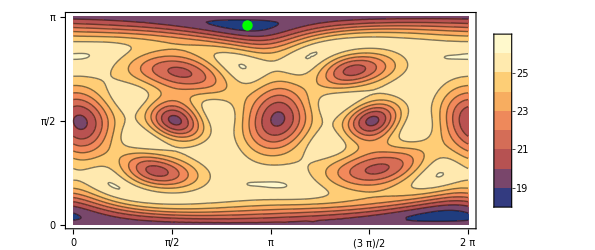

P(T, 𝒱_XISO(U_0)) = (50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)  (a closest elastic map to T having symmetry at least XISO)

```mathematica
MatrixNote[Tmat]
Sig1=TET;
Sig2=XISO;
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TXISO=Closest[Tmat,Sig2];
Tmat1=TTET;
Tmat2=TXISO; 
ListSigma={TET,XISO}; 
ttop = 0.611707;
```

#### Example: Brown TET parabola (supp2) TET to CUBE segment for the Brown map Here TCUBE is the closest to TRIV (Pathway 2), and β_CUBE = 24.34^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TET;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTET=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTET ;
Tmat2=TCUBE;
ListSigma={TET}; *)
```

#### Example: Brown TRIG triangle (supp3) TRIG to CUBE segment for the Brown map Here CUBE is the closest to TRIV (Pathway 2), and β_CUBE = 21.12^o

```mathematica
(* MatrixNote[Tmat]
Sig1=TRIG;
Sig2=CUBE; 
OutputFor[Tmat,Sig1]
TTRIG=Closest[Tmat,Sig1];
OutputFor[Tmat,Sig2]
TCUBE=Closest[Tmat,Sig2];
Tmat1=TTRIG;
Tmat2=TCUBE;
ListSigma={TET,TRIG,MONO};
ttop=0.53515; *)
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### check endpoints (but not that your chosen t values may exclude the endpoints)

```mathematica
MatrixNote[Tmat]
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

T is Brown

(47.8734 | -0.0381235 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381235 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)

(47.8734 | -0.0381235 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381235 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)

(50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)

(50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)

#### t values to use (note: you can choose to use t2 > 1 for the custom set of available maps)

```mathematica
t1 = 1; t2=1.1;dt =0.01;   (* Igel -- show that t > 1 *)
t1 = 0; t2=1;
dt =0.5;
dt = 0.02;
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.42; t2 = 0.44;dt=0.005;  (* Brown TET triangle - Pathway 2 *)
(* t1 = 0.38; t2 = 0.40;dt = 0.005; *)  (* Brown TET triangle - Pathway 3 *)
t1 = 0.41; t2 = 0.45;dt=0.005; 
Ranget=Range[t1,t2,dt];
(* Ranget=Join[{0},Range[t1,t2,dt],{1}] *)
```

```mathematica
t1 = 11; t2 = 1+tpert[Tmat];dt=0.05; 
Ranget=Range[t1,t2,dt];
```

```mathematica
t1 = 0.; t2 = 1.;dt=0.05; 
(* t1 = -tpert[Tmat]; *)
Ranget=Range[t1,t2,dt];
```

#### min and max values of t (these are used for plotting)

```mathematica
Ranget
tmin=Ranget[[1]]
tmax=Ranget[[Length[Ranget]]]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

0.

1.

#### Display the set of Tmats as BB and as Voigt

```mathematica
MatrixNote[Tmat]
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

T is Brown

t = 0.

The [T]_𝔹𝔹 matrix is (47.8734 | -0.0381235 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381235 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)

The eigenvalues are: {201.974,178.753,60.2611,60.2611,54.947,47.4039}

The Voigt matrix is (69.7013 | 30.6962 | 31.3605 | 0.121856 | 2.03836 | -0.967118
30.6962 | 182.697 | 4.90707 | 3.41481 | -2.54035 | -3.85919
31.3605 | 4.90707 | 181.474 | -3.17236 | 8.50349 | 0.877827
0.121856 | 3.41481 | -3.17236 | 23.9367 | -0.0190618 | -0.72283
2.03836 | -2.54035 | 8.50349 | -0.0190618 | 30.7322 | 0.204608
-0.967118 | -3.85919 | 0.877827 | -0.72283 | 0.204608 | 30.1948)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 122.959   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.435 = 24.9^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.05

The [T]_𝔹𝔹 matrix is (47.999 | -0.127328 | -1.5644 | 3.21128 | 5.84167 | 0.208065
-0.127328 | 61.104 | 0.454051 | -4.16703 | -10.667 | 6.39441
-1.5644 | 0.454051 | 61.413 | -2.74682 | -3.54138 | -3.07192
3.21128 | -4.16703 | -2.74682 | 94.7707 | 45.5703 | 33.5544
5.84167 | -10.667 | -3.54138 | 45.5703 | 149.047 | -19.999
0.208065 | 6.39441 | -3.07192 | 33.5544 | -19.999 | 189.267)

The eigenvalues are: {201.263,176.521,61.3171,59.7256,57.2718,47.5013}

The Voigt matrix is (72.1807 | 31.1171 | 30.7319 | 0.165648 | 1.61473 | -0.903006
31.1171 | 179.595 | 5.50895 | 3.37692 | -2.55231 | -3.64983
30.7319 | 5.50895 | 181.309 | -3.28775 | 8.7691 | 0.790509
0.165648 | 3.37692 | -3.28775 | 23.9995 | -0.0636638 | -0.782202
1.61473 | -2.55231 | 8.7691 | -0.0636638 | 30.552 | 0.227025
-0.903006 | -3.64983 | 0.790509 | -0.782202 | 0.227025 | 30.7065)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 119.89   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.425 = 24.35^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.1

The [T]_𝔹𝔹 matrix is (48.1245 | -0.216532 | -1.68315 | 3.1296 | 5.97832 | 0.118671
-0.216532 | 60.7435 | 0.498885 | -3.75535 | -11.2252 | 6.25562
-1.68315 | 0.498885 | 62.4363 | -2.60157 | -3.28266 | -2.91993
3.1296 | -3.75535 | -2.60157 | 94.0384 | 43.2487 | 31.7781
5.97832 | -11.2252 | -3.28266 | 43.2487 | 148.991 | -19.863
0.118671 | 6.25562 | -2.91993 | 31.7781 | -19.863 | 189.267)

The eigenvalues are: {200.661,174.224,62.3734,59.7252,59.0201,47.597}

The Voigt matrix is (74.66 | 31.5379 | 30.1034 | 0.209441 | 1.19109 | -0.838895
31.5379 | 176.493 | 6.11084 | 3.33904 | -2.56426 | -3.44046
30.1034 | 6.11084 | 181.143 | -3.40314 | 9.03471 | 0.703191
0.209441 | 3.33904 | -3.40314 | 24.0622 | -0.108266 | -0.841573
1.19109 | -2.56426 | 9.03471 | -0.108266 | 30.3717 | 0.249443
-0.838895 | -3.44046 | 0.703191 | -0.841573 | 0.249443 | 31.2182)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 116.913   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.416 = 23.82^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.15

The [T]_𝔹𝔹 matrix is (48.25 | -0.305736 | -1.80189 | 3.04792 | 6.11497 | 0.0292769
-0.305736 | 60.383 | 0.543719 | -3.34366 | -11.7834 | 6.11683
-1.80189 | 0.543719 | 63.4597 | -2.45632 | -3.02395 | -2.76793
3.04792 | -3.34366 | -2.45632 | 93.3062 | 40.9271 | 30.0018
6.11497 | -11.7834 | -3.02395 | 40.9271 | 148.934 | -19.727
0.0292769 | 6.11683 | -2.76793 | 30.0018 | -19.727 | 189.267)

The eigenvalues are: {200.147,171.885,63.4299,61.8768,58.5691,47.6915}

The Voigt matrix is (77.1394 | 31.9588 | 29.4749 | 0.253233 | 0.767449 | -0.774783
31.9588 | 173.391 | 6.71272 | 3.30115 | -2.57621 | -3.2311
29.4749 | 6.71272 | 180.977 | -3.51853 | 9.30031 | 0.615873
0.253233 | 3.30115 | -3.51853 | 24.125 | -0.152868 | -0.900944
0.767449 | -2.57621 | 9.30031 | -0.152868 | 30.1915 | 0.27186
-0.774783 | -3.2311 | 0.615873 | -0.900944 | 0.27186 | 31.7298)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 114.036   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.407 = 23.29^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.2

The [T]_𝔹𝔹 matrix is (48.3756 | -0.39494 | -1.92063 | 2.96624 | 6.25162 | -0.0601168
-0.39494 | 60.0226 | 0.588553 | -2.93197 | -12.3416 | 5.97804
-1.92063 | 0.588553 | 64.483 | -2.31107 | -2.76523 | -2.61594
2.96624 | -2.93197 | -2.31107 | 92.574 | 38.6055 | 28.2255
6.25162 | -12.3416 | -2.76523 | 38.6055 | 148.878 | -19.5911
-0.0601168 | 5.97804 | -2.61594 | 28.2255 | -19.5911 | 189.267)

The eigenvalues are: {199.705,169.531,64.4866,64.0669,58.0257,47.7848}

The Voigt matrix is (79.6187 | 32.3796 | 28.8463 | 0.297026 | 0.34381 | -0.710671
32.3796 | 170.288 | 7.3146 | 3.26326 | -2.58816 | -3.02174
28.8463 | 7.3146 | 180.812 | -3.63391 | 9.56592 | 0.528554
0.297026 | 3.26326 | -3.63391 | 24.1878 | -0.19747 | -0.960315
0.34381 | -2.58816 | 9.56592 | -0.19747 | 30.0113 | 0.294277
-0.710671 | -3.02174 | 0.528554 | -0.960315 | 0.294277 | 32.2415)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 111.266   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.398 = 22.79^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.25

The [T]_𝔹𝔹 matrix is (48.5011 | -0.484144 | -2.03937 | 2.88455 | 6.38826 | -0.149511
-0.484144 | 59.6621 | 0.633387 | -2.52029 | -12.8997 | 5.83925
-2.03937 | 0.633387 | 65.5064 | -2.16582 | -2.50651 | -2.46394
2.88455 | -2.52029 | -2.16582 | 91.8417 | 36.2838 | 26.4492
6.38826 | -12.8997 | -2.50651 | 36.2838 | 148.822 | -19.4551
-0.149511 | 5.83925 | -2.46394 | 26.4492 | -19.4551 | 189.267)

The eigenvalues are: {199.321,167.18,66.2024,65.5433,57.4755,47.877}

The Voigt matrix is (82.0981 | 32.8005 | 28.2178 | 0.340818 | -0.0798286 | -0.64656
32.8005 | 167.186 | 7.91649 | 3.22537 | -2.60012 | -2.81238
28.2178 | 7.91649 | 180.646 | -3.7493 | 9.83153 | 0.441236
0.340818 | 3.22537 | -3.7493 | 24.2505 | -0.242072 | -1.01969
-0.0798286 | -2.60012 | 9.83153 | -0.242072 | 29.831 | 0.316694
-0.64656 | -2.81238 | 0.441236 | -1.01969 | 0.316694 | 32.7532)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 108.611   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.389 = 22.3^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.3

The [T]_𝔹𝔹 matrix is (48.6266 | -0.573348 | -2.15812 | 2.80287 | 6.52491 | -0.238904
-0.573348 | 59.3016 | 0.678222 | -2.1086 | -13.4579 | 5.70046
-2.15812 | 0.678222 | 66.5297 | -2.02057 | -2.2478 | -2.31195
2.80287 | -2.1086 | -2.02057 | 91.1095 | 33.9622 | 24.6729
6.52491 | -13.4579 | -2.2478 | 33.9622 | 148.766 | -19.3191
-0.238904 | 5.70046 | -2.31195 | 24.6729 | -19.3191 | 189.267)

The eigenvalues are: {198.985,164.854,68.2699,66.6003,56.923,47.9682}

The Voigt matrix is (84.5774 | 33.2213 | 27.5893 | 0.384611 | -0.503467 | -0.582448
33.2213 | 164.084 | 8.51837 | 3.18749 | -2.61207 | -2.60302
27.5893 | 8.51837 | 180.48 | -3.86469 | 10.0971 | 0.353918
0.384611 | 3.18749 | -3.86469 | 24.3133 | -0.286674 | -1.07906
-0.503467 | -2.61207 | 10.0971 | -0.286674 | 29.6508 | 0.339111
-0.582448 | -2.60302 | 0.353918 | -1.07906 | 0.339111 | 33.2649)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 106.08   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.381 = 21.83^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.35

The [T]_𝔹𝔹 matrix is (48.7521 | -0.662552 | -2.27686 | 2.72119 | 6.66156 | -0.328298
-0.662552 | 58.9412 | 0.723056 | -1.69691 | -14.0161 | 5.56167
-2.27686 | 0.723056 | 67.5531 | -1.87532 | -1.98908 | -2.15995
2.72119 | -1.69691 | -1.87532 | 90.3772 | 31.6406 | 22.8966
6.66156 | -14.0161 | -1.98908 | 31.6406 | 148.71 | -19.1832
-0.328298 | 5.56167 | -2.15995 | 22.8966 | -19.1832 | 189.267)

The eigenvalues are: {198.687,162.57,70.2581,67.6573,56.3691,48.0583}

The Voigt matrix is (87.0568 | 33.6422 | 26.9607 | 0.428403 | -0.927106 | -0.518336
33.6422 | 160.982 | 9.12025 | 3.1496 | -2.62402 | -2.39365
26.9607 | 9.12025 | 180.315 | -3.98008 | 10.3628 | 0.2666
0.428403 | 3.1496 | -3.98008 | 24.3761 | -0.331276 | -1.13843
-0.927106 | -2.62402 | 10.3628 | -0.331276 | 29.4706 | 0.361528
-0.518336 | -2.39365 | 0.2666 | -1.13843 | 0.361528 | 33.7765)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 103.683   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.373 = 21.38^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.4

The [T]_𝔹𝔹 matrix is (48.8777 | -0.751756 | -2.3956 | 2.63951 | 6.79821 | -0.417692
-0.751756 | 58.5807 | 0.76789 | -1.28523 | -14.5743 | 5.42288
-2.3956 | 0.76789 | 68.5764 | -1.73007 | -1.73036 | -2.00796
2.63951 | -1.28523 | -1.73007 | 89.645 | 29.319 | 21.1202
6.79821 | -14.5743 | -1.73036 | 29.319 | 148.654 | -19.0472
-0.417692 | 5.42288 | -2.00796 | 21.1202 | -19.0472 | 189.267)

The eigenvalues are: {198.422,160.347,72.1549,68.7145,55.8143,48.1474}

The Voigt matrix is (89.5361 | 34.0631 | 26.3322 | 0.472196 | -1.35074 | -0.454225
34.0631 | 157.88 | 9.72213 | 3.11171 | -2.63597 | -2.18429
26.3322 | 9.72213 | 180.149 | -4.09547 | 10.6284 | 0.179281
0.472196 | 3.11171 | -4.09547 | 24.4388 | -0.375878 | -1.1978
-1.35074 | -2.63597 | 10.6284 | -0.375878 | 29.2903 | 0.383945
-0.454225 | -2.18429 | 0.179281 | -1.1978 | 0.383945 | 34.2882)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 101.428   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.366 = 20.95^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.45

The [T]_𝔹𝔹 matrix is (49.0032 | -0.84096 | -2.51434 | 2.55783 | 6.93486 | -0.507086
-0.84096 | 58.2202 | 0.812724 | -0.873541 | -15.1325 | 5.28409
-2.51434 | 0.812724 | 69.5998 | -1.58482 | -1.47165 | -1.85596
2.55783 | -0.873541 | -1.58482 | 88.9128 | 26.9974 | 19.3439
6.93486 | -15.1325 | -1.47165 | 26.9974 | 148.597 | -18.9112
-0.507086 | 5.28409 | -1.85596 | 19.3439 | -18.9112 | 189.267)

The eigenvalues are: {198.184,158.204,73.9463,69.7717,55.2587,48.2354}

The Voigt matrix is (92.0154 | 34.4839 | 25.7037 | 0.515988 | -1.77438 | -0.390113
34.4839 | 154.778 | 10.324 | 3.07382 | -2.64792 | -1.97493
25.7037 | 10.324 | 179.983 | -4.21086 | 10.894 | 0.0919632
0.515988 | 3.07382 | -4.21086 | 24.5016 | -0.42048 | -1.25717
-1.77438 | -2.64792 | 10.894 | -0.42048 | 29.1101 | 0.406362
-0.390113 | -1.97493 | 0.0919632 | -1.25717 | 0.406362 | 34.7999)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 99.3247   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.359 = 20.56^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.5

The [T]_𝔹𝔹 matrix is (49.1287 | -0.930164 | -2.63309 | 2.47615 | 7.07151 | -0.59648
-0.930164 | 57.8598 | 0.857558 | -0.461855 | -15.6907 | 5.1453
-2.63309 | 0.857558 | 70.6231 | -1.43957 | -1.21293 | -1.70397
2.47615 | -0.461855 | -1.43957 | 88.1805 | 24.6758 | 17.5676
7.07151 | -15.6907 | -1.21293 | 24.6758 | 148.541 | -18.7752
-0.59648 | 5.1453 | -1.70397 | 17.5676 | -18.7752 | 189.267)

The eigenvalues are: {197.969,156.161,75.6167,70.829,54.7024,48.3222}

The Voigt matrix is (94.4948 | 34.9048 | 25.0751 | 0.559781 | -2.19802 | -0.326001
34.9048 | 151.676 | 10.9259 | 3.03593 | -2.65988 | -1.76557
25.0751 | 10.9259 | 179.818 | -4.32625 | 11.1596 | 0.00464492
0.559781 | 3.03593 | -4.32625 | 24.5644 | -0.465082 | -1.31654
-2.19802 | -2.65988 | 11.1596 | -0.465082 | 28.9299 | 0.428779
-0.326001 | -1.76557 | 0.00464492 | -1.31654 | 0.428779 | 35.3116)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 97.384   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.352 = 20.19^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.55

The [T]_𝔹𝔹 matrix is (49.2543 | -1.01937 | -2.75183 | 2.39447 | 7.20816 | -0.685873
-1.01937 | 57.4993 | 0.902392 | -0.0501683 | -16.2489 | 5.00651
-2.75183 | 0.902392 | 71.6465 | -1.29432 | -0.954215 | -1.55197
2.39447 | -0.0501683 | -1.29432 | 87.4483 | 22.3542 | 15.7913
7.20816 | -16.2489 | -0.954215 | 22.3542 | 148.485 | -18.6393
-0.685873 | 5.00651 | -1.55197 | 15.7913 | -18.6393 | 189.267)

The eigenvalues are: {197.775,154.238,77.1482,71.8864,54.1453,48.4077}

The Voigt matrix is (96.9741 | 35.3256 | 24.4466 | 0.603573 | -2.62166 | -0.261889
35.3256 | 148.574 | 11.5278 | 2.99805 | -2.67183 | -1.55621
24.4466 | 11.5278 | 179.652 | -4.44164 | 11.4252 | -0.0826733
0.603573 | 2.99805 | -4.44164 | 24.6271 | -0.509684 | -1.37591
-2.62166 | -2.67183 | 11.4252 | -0.509684 | 28.7497 | 0.451196
-0.261889 | -1.55621 | -0.0826733 | -1.37591 | 0.451196 | 35.8232)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 95.6154   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.346 = 19.85^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.6

The [T]_𝔹𝔹 matrix is (49.3798 | -1.10857 | -2.87057 | 2.31279 | 7.34481 | -0.775267
-1.10857 | 57.1388 | 0.947226 | 0.361518 | -16.8071 | 4.86772
-2.87057 | 0.947226 | 72.6698 | -1.14907 | -0.695498 | -1.39998
2.31279 | 0.361518 | -1.14907 | 86.716 | 20.0326 | 14.015
7.34481 | -16.8071 | -0.695498 | 20.0326 | 148.429 | -18.5033
-0.775267 | 4.86772 | -1.39998 | 14.015 | -18.5033 | 189.267)

The eigenvalues are: {197.597,152.458,78.5214,72.9438,53.5876,48.492}

The Voigt matrix is (99.4535 | 35.7465 | 23.8181 | 0.647366 | -3.0453 | -0.197778
35.7465 | 145.472 | 12.1297 | 2.96016 | -2.68378 | -1.34684
23.8181 | 12.1297 | 179.487 | -4.55703 | 11.6908 | -0.169992
0.647366 | 2.96016 | -4.55703 | 24.6899 | -0.554286 | -1.43529
-3.0453 | -2.68378 | 11.6908 | -0.554286 | 28.5694 | 0.473613
-0.197778 | -1.34684 | -0.169992 | -1.43529 | 0.473613 | 36.3349)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 94.0284   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.341 = 19.54^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.65

The [T]_𝔹𝔹 matrix is (49.5053 | -1.19778 | -2.98931 | 2.23111 | 7.48146 | -0.864661
-1.19778 | 56.7784 | 0.992061 | 0.773205 | -17.3652 | 4.72893
-2.98931 | 0.992061 | 73.6931 | -1.00382 | -0.436782 | -1.24798
2.23111 | 0.773205 | -1.00382 | 85.9838 | 17.711 | 12.2387
7.48146 | -17.3652 | -0.436782 | 17.711 | 148.373 | -18.3673
-0.864661 | 4.72893 | -1.24798 | 12.2387 | -18.3673 | 189.267)

The eigenvalues are: {197.436,150.844,79.7149,74.0012,53.0293,48.5749}

The Voigt matrix is (101.933 | 36.1673 | 23.1896 | 0.691158 | -3.46894 | -0.133666
36.1673 | 142.369 | 12.7315 | 2.92227 | -2.69573 | -1.13748
23.1896 | 12.7315 | 179.321 | -4.67242 | 11.9564 | -0.25731
0.691158 | 2.92227 | -4.67242 | 24.7527 | -0.598888 | -1.49466
-3.46894 | -2.69573 | 11.9564 | -0.598888 | 28.3892 | 0.49603
-0.133666 | -1.13748 | -0.25731 | -1.49466 | 0.49603 | 36.8466)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 92.6325   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.336 = 19.28^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.7

The [T]_𝔹𝔹 matrix is (49.6309 | -1.28698 | -3.10806 | 2.14943 | 7.6181 | -0.954055
-1.28698 | 56.4179 | 1.03689 | 1.18489 | -17.9234 | 4.59014
-3.10806 | 1.03689 | 74.7165 | -0.858566 | -0.178065 | -1.09599
2.14943 | 1.18489 | -0.858566 | 85.2516 | 15.3894 | 10.4624
7.6181 | -17.9234 | -0.178065 | 15.3894 | 148.317 | -18.2314
-0.954055 | 4.59014 | -1.09599 | 10.4624 | -18.2314 | 189.267)

The eigenvalues are: {197.289,149.419,80.7068,75.0587,52.4703,48.6562}

The Voigt matrix is (104.412 | 36.5882 | 22.561 | 0.73495 | -3.89258 | -0.0695543
36.5882 | 139.267 | 13.3334 | 2.88438 | -2.70769 | -0.92812
22.561 | 13.3334 | 179.155 | -4.78781 | 12.222 | -0.344628
0.73495 | 2.88438 | -4.78781 | 24.8154 | -0.64349 | -1.55403
-3.89258 | -2.70769 | 12.222 | -0.64349 | 28.209 | 0.518447
-0.0695543 | -0.92812 | -0.344628 | -1.55403 | 0.518447 | 37.3582)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 91.4363   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.332 = 19.045^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.75

The [T]_𝔹𝔹 matrix is (49.7564 | -1.37618 | -3.2268 | 2.06775 | 7.75475 | -1.04345
-1.37618 | 56.0574 | 1.08173 | 1.59658 | -18.4816 | 4.45135
-3.2268 | 1.08173 | 75.7398 | -0.713316 | 0.0806511 | -0.94399
2.06775 | 1.59658 | -0.713316 | 84.5193 | 13.0677 | 8.68609
7.75475 | -18.4816 | 0.0806511 | 13.0677 | 148.26 | -18.0954
-1.04345 | 4.45135 | -0.94399 | 8.68609 | -18.0954 | 189.267)

The eigenvalues are: {197.154,148.208,81.4751,76.1163,51.9106,48.7359}

The Voigt matrix is (106.892 | 37.009 | 21.9325 | 0.778743 | -4.31622 | -0.00544261
37.009 | 136.165 | 13.9353 | 2.84649 | -2.71964 | -0.718758
21.9325 | 13.9353 | 178.99 | -4.90319 | 12.4876 | -0.431946
0.778743 | 2.84649 | -4.90319 | 24.8782 | -0.688092 | -1.6134
-4.31622 | -2.71964 | 12.4876 | -0.688092 | 28.0287 | 0.540864
-0.00544261 | -0.718758 | -0.431946 | -1.6134 | 0.540864 | 37.8699)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 90.4479   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.329 = 18.85^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.8

The [T]_𝔹𝔹 matrix is (49.8819 | -1.46539 | -3.34554 | 1.98607 | 7.8914 | -1.13284
-1.46539 | 55.697 | 1.12656 | 2.00826 | -19.0398 | 4.31257
-3.34554 | 1.12656 | 76.7632 | -0.568065 | 0.339368 | -0.791995
1.98607 | 2.00826 | -0.568065 | 83.7871 | 10.7461 | 6.90978
7.8914 | -19.0398 | 0.339368 | 10.7461 | 148.204 | -17.9594
-1.13284 | 4.31257 | -0.791995 | 6.90978 | -17.9594 | 189.267)

The eigenvalues are: {197.031,147.232,81.9996,77.1738,51.3502,48.8137}

The Voigt matrix is (109.371 | 37.4299 | 21.304 | 0.822535 | -4.73985 | 0.0586691
37.4299 | 133.063 | 14.5372 | 2.80861 | -2.73159 | -0.509396
21.304 | 14.5372 | 178.824 | -5.01858 | 12.7532 | -0.519264
0.822535 | 2.80861 | -5.01858 | 24.941 | -0.732694 | -1.67277
-4.73985 | -2.73159 | 12.7532 | -0.732694 | 27.8485 | 0.563281
0.0586691 | -0.509396 | -0.519264 | -1.67277 | 0.563281 | 38.3816)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 89.6741   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.326 = 18.7^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.85

The [T]_𝔹𝔹 matrix is (50.0075 | -1.55459 | -3.46428 | 1.90439 | 8.02805 | -1.22224
-1.55459 | 55.3365 | 1.1714 | 2.41995 | -19.598 | 4.17378
-3.46428 | 1.1714 | 77.7865 | -0.422815 | 0.598084 | -0.639999
1.90439 | 2.41995 | -0.422815 | 83.0548 | 8.42453 | 5.13347
8.02805 | -19.598 | 0.598084 | 8.42453 | 148.148 | -17.8235
-1.22224 | 4.17378 | -0.639999 | 5.13347 | -17.8235 | 189.267)

The eigenvalues are: {196.919,146.507,82.2632,78.2314,50.7891,48.8895}

The Voigt matrix is (111.85 | 37.8507 | 20.6754 | 0.866328 | -5.16349 | 0.122781
37.8507 | 129.961 | 15.1391 | 2.77072 | -2.74354 | -0.300034
20.6754 | 15.1391 | 178.658 | -5.13397 | 13.0188 | -0.606583
0.866328 | 2.77072 | -5.13397 | 25.0037 | -0.777296 | -1.73214
-5.16349 | -2.74354 | 13.0188 | -0.777296 | 27.6683 | 0.585699
0.122781 | -0.300034 | -0.606583 | -1.73214 | 0.585699 | 38.8933)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 89.1205   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.325 = 18.6^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.9

The [T]_𝔹𝔹 matrix is (50.133 | -1.6438 | -3.58303 | 1.82271 | 8.1647 | -1.31163
-1.6438 | 54.976 | 1.21623 | 2.83164 | -20.1562 | 4.03499
-3.58303 | 1.21623 | 78.8099 | -0.277565 | 0.856801 | -0.488004
1.82271 | 2.83164 | -0.277565 | 82.3226 | 6.10292 | 3.35716
8.1647 | -20.1562 | 0.856801 | 6.10292 | 148.092 | -17.6875
-1.31163 | 4.03499 | -0.488004 | 3.35716 | -17.6875 | 189.267)

The eigenvalues are: {196.818,146.048,82.2543,79.2891,50.2273,48.9629}

The Voigt matrix is (114.33 | 38.2716 | 20.0469 | 0.91012 | -5.58713 | 0.186892
38.2716 | 126.859 | 15.741 | 2.73283 | -2.75549 | -0.0906722
20.0469 | 15.741 | 178.493 | -5.24936 | 13.2845 | -0.693901
0.91012 | 2.73283 | -5.24936 | 25.0665 | -0.821898 | -1.79151
-5.58713 | -2.75549 | 13.2845 | -0.821898 | 27.488 | 0.608116
0.186892 | -0.0906722 | -0.693901 | -1.79151 | 0.608116 | 39.4049)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 88.7912   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.323 = 18.53^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 0.95

The [T]_𝔹𝔹 matrix is (50.2585 | -1.733 | -3.70177 | 1.74103 | 8.30135 | -1.40102
-1.733 | 54.6156 | 1.26107 | 3.24332 | -20.7144 | 3.8962
-3.70177 | 1.26107 | 79.8332 | -0.132314 | 1.11552 | -0.336009
1.74103 | 3.24332 | -0.132314 | 81.5904 | 3.78131 | 1.58085
8.30135 | -20.7144 | 1.11552 | 3.78131 | 148.036 | -17.5515
-1.40102 | 3.8962 | -0.336009 | 1.58085 | -17.5515 | 189.267)

The eigenvalues are: {196.727,145.86,81.9673,80.3467,49.6647,49.0336}

The Voigt matrix is (116.809 | 38.6924 | 19.4184 | 0.953913 | -6.01077 | 0.251004
38.6924 | 123.757 | 16.3428 | 2.69494 | -2.76745 | 0.11869
19.4184 | 16.3428 | 178.327 | -5.36475 | 13.5501 | -0.781219
0.953913 | 2.69494 | -5.36475 | 25.1293 | -0.8665 | -1.85088
-6.01077 | -2.76745 | 13.5501 | -0.8665 | 27.3078 | 0.630533
0.251004 | 0.11869 | -0.781219 | -1.85088 | 0.630533 | 39.9166)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 88.6886   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.323 = 18.51^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

t = 1.

The [T]_𝔹𝔹 matrix is (50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)

The eigenvalues are: {196.646,145.942,81.4044,81.4044,49.1012,49.1012}

The Voigt matrix is (119.288 | 39.1133 | 18.7898 | 0.997705 | -6.43441 | 0.315116
39.1133 | 120.655 | 16.9447 | 2.65705 | -2.7794 | 0.328052
18.7898 | 16.9447 | 178.161 | -5.48014 | 13.8157 | -0.868537
0.997705 | 2.65705 | -5.48014 | 25.192 | -0.911102 | -1.91026
-6.43441 | -2.7794 | 13.8157 | -0.911102 | 27.1276 | 0.65295
0.315116 | 0.328052 | -0.868537 | -1.91026 | 0.65295 | 40.4283)

11-22-2023 17:34

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 88.8137   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.324 = 18.54^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Optional: Choose an orientation for all the balls based on the closest XISO (or whatever you want).

#### commands copied from LatticeOfClosestMaps.nb Display the set of REORIENTED Tmats as BB and as Voigt

```mathematica
(* WantDetails="WantDetails";
OutputFor[Tmat,XISO]
MatrixForm[UT[Tmat,XISO]]
MatrixForm[Closest[Tmat,XISO]]
OutputFor[Closest[Tmat,XISO],XISO]
Ux=IdentityMatrix[3];
(* Ux=UT[Closest[Tmat,XISO],XISO]; *)
MatrixForm[Ux]
Ubarx=MatrixUbar[Ux];
MatrixForm[Chop[Ubarx,.0001]]
(Print["t = ",# ]; PrintVoigt[Transpose[Ubarx].TT[#,Tmat1,Tmat2].Ubarx])&/@Ranget *)
```

## Proceed with Tmat in its original orientation

```mathematica
Ux=IdentityMatrix[3];
Ubarx=MatrixUbar[Ux];
```

## Example functions (none of these are needed)

#### Example of plotting two sets of points on one plot.

```mathematica
fff[t_,Sigma_]:=t/2
```

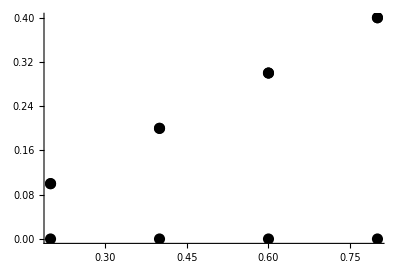

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,fff[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,fff[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Examples: Closest to MONO for some chosen t (not necessarily the t in Ranget)

t = 0.2

11-22-2023 17:34

NMinimize = {0.497121,{θ→1.61321,σ→-2.36914,ϕ→1.53964}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {92.4,0.,88.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.00132074 | -0.999101 | -0.0423766
0.0311236 | -0.0423972 | 0.998616
-0.999515 | 0 | 0.0311516)  (A MONO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

𝒱_MONO(U_0)contains a closest map to T in 𝒯_MONO

d(T, 𝒯_MONO) = 0.497 (Distance from T to 𝒯_MONO)

β_MONO^T = 0.00173 = 0.1^o (Angle betweem T and 𝒯_MONO)

Does the green point look like a correct GLOBAL minimum? If not, the minimization has failed.

Uniqueness (or not) of the closest MONO map is usually obvious from the contour plot.

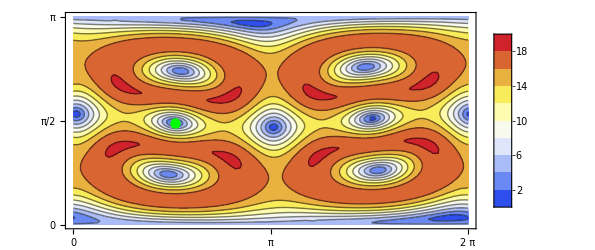

P(T, 𝒱_MONO(U_0)) = (48.387 | -0.302995 | -1.95096 | 3.21055 | 6.14272 | 0.0784719
-0.302995 | 60.0065 | 0.458536 | -2.95491 | -12.3434 | 5.97307
-1.95096 | 0.458536 | 64.4829 | -2.26153 | -2.8112 | -2.58645
3.21055 | -2.95491 | -2.26153 | 92.5669 | 38.5916 | 28.2236
6.14272 | -12.3434 | -2.8112 | 38.5916 | 148.89 | -19.5985
0.0784719 | 5.97307 | -2.58645 | 28.2236 | -19.5985 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

```mathematica
tpicks ={0,1,tmax};
tpicks={0.2};
Sigma=MONO;
(* OutputFor[TT[#,Tmat1,Tmat2],Sigma]&/@tpicks *)
Do[(Print["t = ",tpicks[[i]]];OutputFor[TT[tpicks[[i]],Tmat1,Tmat2],Sigma]),{i,1,Length[tpicks]}]
```

#### Test Tmat (from above)

```mathematica
Ttest=TT[tpicks[[Length[tpicks]]],Tmat1,Tmat2];
MatrixForm[Ttest]
```

(48.3756 | -0.39494 | -1.92063 | 2.96624 | 6.25162 | -0.0601168
-0.39494 | 60.0226 | 0.588553 | -2.93197 | -12.3416 | 5.97804
-1.92063 | 0.588553 | 64.483 | -2.31107 | -2.76523 | -2.61594
2.96624 | -2.93197 | -2.31107 | 92.574 | 38.6055 | 28.2255
6.25162 | -12.3416 | -2.76523 | 38.6055 | 148.878 | -19.5911
-0.0601168 | 5.97804 | -2.61594 | 28.2255 | -19.5911 | 189.267)

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

(-0.00132074 | -0.999101 | -0.0423766
0.0311236 | -0.0423972 | 0.998616
-0.999515 | 0. | 0.0311516)

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

(48.387 | -0.302995 | -1.95096 | 3.21055 | 6.14272 | 0.0784719
-0.302995 | 60.0065 | 0.458536 | -2.95491 | -12.3434 | 5.97307
-1.95096 | 0.458536 | 64.4829 | -2.26153 | -2.8112 | -2.58645
3.21055 | -2.95491 | -2.26153 | 92.5669 | 38.5916 | 28.2236
6.14272 | -12.3434 | -2.8112 | 38.5916 | 148.89 | -19.5985
0.0784719 | 5.97307 | -2.58645 | 28.2236 | -19.5985 | 189.267)

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
βT[Ttest,MONO]/Degree
```

0.099143

0.099143

## Calculate distance to each symmetry class KEY COMMAND: OutputFor performs the key calculations (minimizations)

```mathematica
WantDetails="NoWantDetails";
```

```mathematica
Ranget
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
ListSigma
```

{TET,XISO}

```mathematica
(* OutputFor[TT[Ranget[[1]],Tmat1,Tmat2],ListSigma[[1]]] *) (* example of one OutputFor *)
```

```mathematica
Do[(Print["t = ",Ranget[[i]]];OutputFor[TT[Ranget[[i]],Tmat1,Tmat2],#])&/@ListSigma,{i,1,Length[Ranget]}]
```

t = 0.

11-22-2023 17:35

NMinimize = {1.34343×10^-6,{θ→0.0454989,σ→2.38367,ϕ→1.66271}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,136.6,95.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0353227 | 0.0960596 | 0.994749
0.689737 | -0.722642 | 0.0452912
0.723198 | 0.684515 | -0.0917815)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.

11-22-2023 17:36

NMinimize = {88.825,{θ→6.03778,σ→0.111617,ϕ→0.0959178}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {345.9,0.,5.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.965579 | 0.242954 | 0.0929013
-0.241837 | 0.970038 | -0.0232679
-0.0957708 | 0 | 0.995403)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.05

11-22-2023 17:36

NMinimize = {2.70822,{θ→0.045494,σ→0.0283592,ϕ→1.66424}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,1.6,95.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0944668 | -0.0428169 | 0.994607
0.0240841 | 0.998684 | 0.0452799
-0.995237 | 0.0282317 | -0.0933112)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.05

11-22-2023 17:37

NMinimize = {84.3842,{θ→2.89238,σ→1.7922,ϕ→3.04319}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {165.7,0.,174.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.964418 | -0.246641 | -0.0952122
-0.245448 | -0.969107 | 0.0242318
-0.0982474 | 0 | -0.995162)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.1

11-22-2023 17:37

NMinimize = {5.41631,{θ→0.0454919,σ→0.0292781,ϕ→1.66582}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,1.7,95.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0960685 | -0.0426822 | 0.994459
0.0249309 | 0.998664 | 0.0452711
-0.995062 | 0.0291419 | -0.094876)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.1

11-22-2023 17:37

NMinimize = {79.9431,{θ→2.88818,σ→-0.685757,ϕ→3.04081}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {165.5,0.,174.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.963151 | -0.250706 | -0.0973957
-0.249434 | -0.968063 | 0.0252232
-0.100609 | 0 | -0.994926)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.15

11-22-2023 17:38

NMinimize = {8.12433,{θ→0.0454923,σ→-0.755167,ϕ→1.66742}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,-43.3,95.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0390025 | -0.0991673 | 0.994306
-0.687896 | 0.724397 | 0.0452645
-0.724761 | -0.682214 | -0.09647)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.15

11-22-2023 17:38

NMinimize = {75.5016,{θ→2.88362,σ→-2.36917,ϕ→3.03855}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {165.2,0.,174.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.961781 | -0.255117 | -0.0994607
-0.253764 | -0.96691 | 0.0262424
-0.102864 | 0 | -0.994695)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.2

11-22-2023 17:39

NMinimize = {10.8324,{θ→3.18709,σ→1.53958,ϕ→1.47255}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,88.2,84.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0423986 | 0.0993571 | -0.994148
-0.998618 | -0.0267237 | -0.04526
-0.0310642 | 0.994693 | 0.0980867)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.2

11-22-2023 17:39

NMinimize = {71.0598,{θ→2.87873,σ→-2.36653,ϕ→3.03638}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {164.9,0.,174.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.96031 | -0.259847 | -0.101415
-0.25841 | -0.96565 | 0.0272899
-0.105023 | 0 | -0.99447)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.25

11-22-2023 17:39

NMinimize = {13.5405,{θ→3.18709,σ→-0.0322465,ϕ→1.47091}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,-1.8,84.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.10103 | 0.0422489 | -0.993986
0.0276743 | -0.998592 | -0.0452575
-0.994498 | -0.0320802 | 0.0997186)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.25

11-22-2023 17:40

NMinimize = {66.6179,{θ→2.87352,σ→2.83324,ϕ→3.03429}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {164.6,0.,173.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.958737 | -0.264875 | -0.103267
-0.263351 | -0.964283 | 0.0283661
-0.107093 | 0 | -0.994249)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.3

11-22-2023 17:40

NMinimize = {16.2488,{θ→3.1871,σ→-0.033313,ϕ→1.46926}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,-1.9,84.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.102712 | 0.0420933 | -0.99382
0.0286641 | -0.998564 | -0.0452566
-0.994298 | -0.0331354 | 0.101358)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.3

11-22-2023 17:41

NMinimize = {62.1758,{θ→2.86801,σ→2.83316,ϕ→3.03229}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {164.3,0.,173.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.957064 | -0.270182 | -0.105024
-0.26857 | -0.962809 | 0.0294716
-0.109081 | 0 | -0.994033)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.35

11-22-2023 17:41

NMinimize = {18.9573,{θ→3.18711,σ→-0.0344218,ϕ→1.46762}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,-2.,84.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.104394 | 0.0419311 | -0.993652
0.0296959 | -0.998534 | -0.045257
-0.994093 | -0.034232 | 0.102996)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.35

11-22-2023 17:41

NMinimize = {57.7336,{θ→6.00381,σ→0.111631,ϕ→0.111223}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {344.,0.,6.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.955289 | 0.275755 | 0.106691
-0.274051 | 0.961228 | -0.0306072
-0.110994 | 0 | 0.993821)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.4

11-22-2023 17:42

NMinimize = {21.6663,{θ→0.0455237,σ→-1.53522,ϕ→1.67561}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,-88.,96.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0417618 | -0.106067 | 0.993482
-0.998501 | 0.0307726 | 0.0452582
-0.0353724 | -0.993883 | -0.104623)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.4

11-22-2023 17:42

NMinimize = {53.2913,{θ→5.99774,σ→0.111516,ϕ→0.113081}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {343.6,0.,6.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.953409 | 0.28158 | 0.108274
-0.279782 | 0.959538 | -0.0317735
-0.11284 | 0 | 0.993613)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.45

11-22-2023 17:43

NMinimize = {24.3756,{θ→3.18713,σ→-0.0367755,ϕ→1.46436}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,-2.1,83.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.107723 | 0.0415847 | -0.993311
0.031897 | -0.998466 | -0.0452597
-0.993669 | -0.0365592 | 0.106231)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.45

11-22-2023 17:43

NMinimize = {48.8491,{θ→5.99142,σ→0.111522,ϕ→0.114877}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {343.3,0.,6.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.951424 | 0.287648 | 0.10978
-0.285752 | 0.957736 | -0.0329715
-0.114624 | 0 | 0.993409)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.5

11-22-2023 17:43

NMinimize = {27.0856,{θ→0.0455418,σ→-0.747372,ϕ→1.67882}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,-42.8,96.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.04805 | -0.106597 | 0.993141
-0.682609 | 0.729381 | 0.0452608
-0.729202 | -0.675752 | -0.107811)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.5

11-22-2023 17:44

NMinimize = {44.407,{θ→5.98483,σ→0.111619,ϕ→0.116617}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {342.9,0.,6.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.949329 | 0.29395 | 0.111212
-0.291953 | 0.955821 | -0.0342019
-0.116353 | 0 | 0.993208)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.55

11-22-2023 17:44

NMinimize = {29.7961,{θ→3.18714,σ→-0.0393291,ϕ→1.46123}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {182.6,-2.3,83.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.110944 | 0.0412034 | -0.992972
0.0343029 | -0.998386 | -0.0452607
-0.993234 | -0.0390832 | 0.109352)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.55

11-22-2023 17:45

NMinimize = {39.9649,{θ→5.97799,σ→2.95968,ϕ→0.118307}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {342.5,0.,6.8})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.947122 | 0.300479 | 0.112576
-0.298378 | 0.953789 | -0.0354657
-0.118031 | 0 | 0.99301)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.6

11-22-2023 17:45

NMinimize = {32.5074,{θ→0.0455551,σ→-0.74471,ϕ→1.68187}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {2.6,-42.7,96.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0505541 | -0.108533 | 0.992807
-0.680767 | 0.731101 | 0.0452587
-0.730754 | -0.673582 | -0.110846)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.6

11-22-2023 17:45

NMinimize = {35.5231,{θ→5.97091,σ→0.111532,ϕ→0.119951}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {342.1,0.,6.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.944798 | 0.307228 | 0.113876
-0.305021 | 0.951636 | -0.0367641
-0.119664 | 0 | 0.992814)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.65

11-22-2023 17:46

NMinimize = {29.8382,{θ→5.96477,σ→1.93256,ϕ→0.121605}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {341.8,110.7,7.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0408462 | -0.992501 | 0.115207
0.998243 | -0.0454907 | -0.0379765
0.0429326 | 0.113454 | 0.992615)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.65

11-22-2023 17:46

NMinimize = {31.0814,{θ→2.82199,σ→-1.44197,ϕ→3.02004}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {161.7,0.,173.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.942354 | -0.314194 | -0.115116
-0.311875 | -0.949359 | 0.0380982
-0.121257 | 0 | -0.992621)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.7

11-22-2023 17:46

NMinimize = {25.5746,{θ→5.95694,σ→-0.415934,ϕ→0.123159}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {341.3,-23.8,7.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.730436 | 0.672995 | 0.116368
-0.673673 | 0.73798 | -0.0393709
-0.112373 | -0.0496359 | 0.992426)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.7

11-22-2023 17:47

NMinimize = {26.6401,{θ→5.95601,σ→3.11036,ϕ→0.123125}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {341.3,0.,7.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.939785 | 0.321371 | 0.1163
-0.318938 | 0.946953 | -0.039469
-0.122815 | 0 | 0.99243)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.75

11-22-2023 17:47

NMinimize = {21.3113,{θ→2.8073,σ→-1.16279,ϕ→3.01691}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {160.8,-66.6,172.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.673078 | 0.730182 | -0.117478
0.737924 | -0.67365 | 0.0408036
-0.0493449 | -0.114154 | -0.992237)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.75

11-22-2023 17:48

NMinimize = {22.199,{θ→5.9482,σ→0.111619,ϕ→0.124664}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {340.8,0.,7.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.937086 | 0.328756 | 0.11743
-0.326205 | 0.944415 | -0.0408781
-0.124342 | 0 | 0.992239)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.8

11-22-2023 17:48

NMinimize = {17.0483,{θ→5.94062,σ→-0.399873,ϕ→0.126189}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {340.4,-22.9,7.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.729924 | 0.673171 | 0.118541
-0.673626 | 0.737862 | -0.0422748
-0.115925 | -0.0489952 | 0.992049)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.8

11-22-2023 17:49

NMinimize = {17.7583,{θ→5.94015,σ→0.111544,ϕ→0.126177}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {340.3,0.,7.2})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.934252 | 0.336347 | 0.11851
-0.333673 | 0.941738 | -0.0423267
-0.125842 | 0 | 0.99205)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.85

11-22-2023 17:49

NMinimize = {12.7856,{θ→5.93214,σ→2.75006,ϕ→0.127673}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {339.9,157.6,7.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.729663 | -0.673273 | 0.119562
0.673603 | -0.737796 | -0.0437847
0.117691 | 0.0485889 | 0.991861)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.85

11-22-2023 17:49

NMinimize = {13.318,{θ→5.93186,σ→-0.00430089,ϕ→0.127667}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {339.9,0.,7.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.931277 | 0.34414 | 0.119544
-0.341339 | 0.938918 | -0.0438163
-0.127321 | 0 | 0.991862)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.9

11-22-2023 17:50

NMinimize = {8.52333,{θ→5.92347,σ→2.75859,ϕ→0.129143}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {339.4,158.1,7.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.729399 | -0.673385 | 0.120541
0.673579 | -0.737724 | -0.0453333
0.119453 | 0.048128 | 0.991673)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.9

11-22-2023 17:50

NMinimize = {8.87814,{θ→5.92334,σ→2.95843,ϕ→0.129141}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {339.4,0.,7.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.928156 | 0.352134 | 0.120533
-0.349201 | 0.93595 | -0.0453484
-0.128782 | 0 | 0.991673)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 0.95

11-22-2023 17:51

NMinimize = {4.26145,{θ→5.9146,σ→1.9819,ϕ→0.1306}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {338.9,113.6,7.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0393326 | -0.991814 | 0.121483
0.99787 | -0.0453199 | -0.0469207
0.0520422 | 0.119379 | 0.991484)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 0.95

11-22-2023 17:51

NMinimize = {4.43879,{θ→5.91457,σ→-0.00430738,ϕ→0.1306}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {338.9,0.,7.5})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.924883 | 0.360325 | 0.121481
-0.357257 | 0.932827 | -0.0469248
-0.130229 | 0 | 0.991484)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

t = 1.

11-22-2023 17:51

NMinimize = {4.87482×10^-7,{θ→2.76397,σ→-1.14342,ϕ→3.00954}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {158.4,-65.5,172.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.717478 | 0.685745 | -0.12239
0.69444 | -0.717911 | 0.0485472
-0.0545739 | -0.119824 | -0.991294)  (A TET-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

t = 1.

11-22-2023 17:52

NMinimize = {4.59046×10^-7,{θ→5.90556,σ→0.111619,ϕ→0.13205}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {338.4,0.,7.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.921451 | 0.368714 | 0.12239
-0.365504 | 0.929543 | -0.0485472
-0.131666 | 0 | 0.991294)  (A XISO-minimizer for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

## Optional: Plot the balls (this was motivated by the Brown TET triangle)

```mathematica
eye=10xyzTP[{30Degree,75Degree}];
plotpoints=10;
```

#### overwrite the default coloring for this Tmat (see chooseTmat.nb) cpMONO is in common_funs.nb; it requires defining the contours

```mathematica
Clear[contours,MaxForScaling]
```

```mathematica
contours[Tmat]=Range[0,20,2]
MaxForScaling[Tmat]=20
```

{0,2,4,6,8,10,12,14,16,18,20}

20

```mathematica
(* Show[cpMONO[TT[Ranget[[1]],Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye] *)
```

#### function for plotting the U matrix (columns) For Sigma ≠ TRIV, Udots[Tmat, Sigma] should give the high symmetry axis (green) of a closest Sigma map to Tmat. For Sigma ≠ TRIV, MONO, Udots[Tmat, Sigma] should also give 2-fold axes (red, blue) of a closest Sigma map to Tmat.

```mathematica
Udots[Tmat_,Sigma_]:=Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.03],{ 
{Red,     Point[UT[Tmat, Sigma].{1,0,0}],Point[UT[Tmat, Sigma].{-1,0,0}]},
{Blue,   Point[UT[Tmat, Sigma].{0,1,0}],Point[UT[Tmat, Sigma].{0,-1,0}]},
{Green,Point[UT[Tmat, Sigma].{0,0,1}],Point[UT[Tmat, Sigma].{0,0,-1}]}}},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

#### main plot (Sig1 and Sig2 should be specified at the top)

```mathematica
If[Length[Ranget] <12,
{Show[cpMONO[TT[#,Tmat1,Tmat2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget;
Udots[TT[#,Tmat1,Tmat2],Sig1]&/@Ranget;
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig1],  contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget; 
Show[cpMONO[Closest[TT[#,Tmat1,Tmat2],Sig2],contours[Tmat],MaxForScaling[Tmat]],Boxed->False,Lighting->{{"Ambient",White}},ViewPoint->eye]&/@Ranget}]
```

#### plot the U dots on a pair of plots for points on either side of the triangle (ttop should be specified at the top)

```mathematica
Ranget
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
Ranget1=Select[Ranget,#<=ttop&]    (* Note ≤ *)
Ranget2=Select[Ranget,#>ttop&]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6}

{0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
ListMat1=TT[#,Tmat1,Tmat2]&/@Ranget1;
ListMat2=TT[#,Tmat1,Tmat2]&/@Ranget2;
```

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
MatrixForm[UT[#,Sig1]]&/@ListMat1
Print["Ranget2 = ",Ranget2];
MatrixForm[UT[#,Sig1]]&/@ListMat2
```

T is Brown

Ranget1 = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6}

{(0.0353227 | 0.0960596 | 0.994749
0.689737 | -0.722642 | 0.0452912
0.723198 | 0.684515 | -0.0917815),(-0.0944668 | -0.0428169 | 0.994607
0.0240841 | 0.998684 | 0.0452799
-0.995237 | 0.0282317 | -0.0933112),(-0.0960685 | -0.0426822 | 0.994459
0.0249309 | 0.998664 | 0.0452711
-0.995062 | 0.0291419 | -0.094876),(-0.0390025 | -0.0991673 | 0.994306
-0.687896 | 0.724397 | 0.0452645
-0.724761 | -0.682214 | -0.09647),(0.0423986 | 0.0993571 | -0.994148
-0.998618 | -0.0267237 | -0.04526
-0.0310642 | 0.994693 | 0.0980867),(-0.10103 | 0.0422489 | -0.993986
0.0276743 | -0.998592 | -0.0452575
-0.994498 | -0.0320802 | 0.0997186),(-0.102712 | 0.0420933 | -0.99382
0.0286641 | -0.998564 | -0.0452566
-0.994298 | -0.0331354 | 0.101358),(-0.104394 | 0.0419311 | -0.993652
0.0296959 | -0.998534 | -0.045257
-0.994093 | -0.034232 | 0.102996),(0.0417618 | -0.106067 | 0.993482
-0.998501 | 0.0307726 | 0.0452582
-0.0353724 | -0.993883 | -0.104623),(-0.107723 | 0.0415847 | -0.993311
0.031897 | -0.998466 | -0.0452597
-0.993669 | -0.0365592 | 0.106231),(-0.04805 | -0.106597 | 0.993141
-0.682609 | 0.729381 | 0.0452608
-0.729202 | -0.675752 | -0.107811),(-0.110944 | 0.0412034 | -0.992972
0.0343029 | -0.998386 | -0.0452607
-0.993234 | -0.0390832 | 0.109352),(-0.0505541 | -0.108533 | 0.992807
-0.680767 | 0.731101 | 0.0452587
-0.730754 | -0.673582 | -0.110846)}

Ranget2 = {0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{(-0.0408462 | -0.992501 | 0.115207
0.998243 | -0.0454907 | -0.0379765
0.0429326 | 0.113454 | 0.992615),(0.730436 | 0.672995 | 0.116368
-0.673673 | 0.73798 | -0.0393709
-0.112373 | -0.0496359 | 0.992426),(0.673078 | 0.730182 | -0.117478
0.737924 | -0.67365 | 0.0408036
-0.0493449 | -0.114154 | -0.992237),(0.729924 | 0.673171 | 0.118541
-0.673626 | 0.737862 | -0.0422748
-0.115925 | -0.0489952 | 0.992049),(-0.729663 | -0.673273 | 0.119562
0.673603 | -0.737796 | -0.0437847
0.117691 | 0.0485889 | 0.991861),(-0.729399 | -0.673385 | 0.120541
0.673579 | -0.737724 | -0.0453333
0.119453 | 0.048128 | 0.991673),(-0.0393326 | -0.991814 | 0.121483
0.99787 | -0.0453199 | -0.0469207
0.0520422 | 0.119379 | 0.991484),(0.717478 | 0.685745 | -0.12239
0.69444 | -0.717911 | 0.0485472
-0.0545739 | -0.119824 | -0.991294)}

```mathematica
MatrixNote[Tmat]
Print["Ranget1 = ",Ranget1];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat1},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
Print["Ranget2 = ",Ranget2];
Graphics3D[{{EdgeForm[],GrayLevel[.8],Polygon/@SpherePolyList[0.99,0,360,0,180,5,5]},
PointSize[.02],{ 
{Red,     Point[UT[#,Sig1].{1,0,0}],Point[UT[#,Sig1].{-1,0,0}]},
{Blue,   Point[UT[#,Sig1].{0,1,0}],Point[UT[#,Sig1].{0,-1,0}]},
{Green,Point[UT[#,Sig1].{0,0,1}],Point[UT[#,Sig1].{0,0,-1}]}}&/@ListMat2},Boxed->False,Lighting->"Neutral",ViewPoint->eye]
```

T is Brown

Ranget1 = {0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6}

-Graphics3D-

Ranget2 = {0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

-Graphics3D-

## Beta curves

```mathematica
ipick =1;
ListSigma
Sigpick=ListSigma[[ipick]]
MatrixNote[Tmat]
Ranget
```

{TET,XISO}

TET

T is Brown

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
ColumnForm[{PaddedForm[#,{2,2}],Round[βT[TT[#,Tmat1,Tmat2],Sigpick]/Degree,.001]}&/@Ranget]
```

{ 0.00,0.}
{ 0.05,0.534}
{ 0.10,1.072}
{ 0.15,1.614}
{ 0.20,2.161}
{ 0.25,2.711}
{ 0.30,3.265}
{ 0.35,3.821}
{ 0.40,4.381}
{ 0.45,4.943}
{ 0.50,5.508}
{ 0.55,6.074}
{ 0.60,6.642}
{ 0.65,6.104}
{ 0.70,5.237}
{ 0.75,4.367}
{ 0.80,3.495}
{ 0.85,2.622}
{ 0.90,1.748}
{ 0.95,0.874}
{ 1.00,0.}

#### Angle in radians between Tmat and the closest-Sigma to Tmat is βT[Tmat, Sigma]

```mathematica
MatrixNote[Tmat]
βT[Tmat,Sigpick]
%/Degree
```

T is Brown

0.137145

7.85784

#### Plot all the beta curves together.

```mathematica
line[Sigma_]:=Line[{#,βT[TT[#,Tmat1,Tmat2],Sigma]/Degree}&/@Ranget];
```

#### This simple plot should always work (With the Closest maps pre-saved, the plotting should be quick.)

```mathematica
(* Ranget *)
```

```mathematica
(* line/@ListSigma *)
```

T is Brown

{TET,XISO}

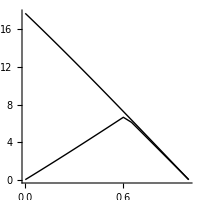

```mathematica
MatrixNote[Tmat]
ListSigma
Graphics[line/@ListSigma,Axes->True,AspectRatio->1,ImageSize->200]
```

#### Or pick only one from ListSigma (see ipick above)

Line[{{0.,0},{0.05,0.533713},{0.1,1.07193},{0.15,1.61439},{0.2,2.16086},{0.25,2.71105},{0.3,3.26469},{0.35,3.82147},{0.4,4.3811},{0.45,4.94326},{0.5,5.50762},{0.55,6.07384},{0.6,6.64156},{0.65,6.10419},{0.7,5.23666},{0.75,4.36685},{0.8,3.49522},{0.85,2.62225},{0.9,1.7484},{0.95,0.874155},{1.,0}}]

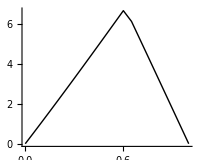

```mathematica
line[Sigpick]
Graphics[line[Sigpick],Axes->True,AspectRatio->.8,ImageSize->200]
```

```mathematica
xran =Ranget[[Length[Ranget]]]-Ranget[[1]]
```

1.

```mathematica
Max[Ranget]
```

1.

```mathematica
Ranget
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

#### The fancier version has colored dots (hues are set in chooseTmat.nb)

```mathematica
PtOnβcurve[t_,Σ_]:={t,βT[TT[t,Tmat1,Tmat2],Σ]/Degree};
BetaCurve[Ranget_,Σ_]:={Point/@Table[PtOnβcurve[Ranget[[n]],Σ],{n,1,Length[Ranget]}]};     
yvals=βT[TT[#,Tmat1,Tmat2],ListSigma[[1]]]/Degree &/@ Ranget; (* based on the first Σ in the list *)
ymin=Min[yvals];
ymax=Max[yvals];
xmin=Min[Ranget];
xmax=Max[Ranget];
xran =xmax-xmin;
btextx=xmin-0.05xran; (* btextx=1.03tmax; *)
ylabelx=xmin-0.35xran; 
ylabely =0.5(ymin+ymax);
xlabelx=(Max[Ranget]+Min[Ranget])/2;
xlabely =-0.1ymax;
```

```mathematica
ListSigma
```

{TET,XISO}

```mathematica
xlabely
```

-0.664156

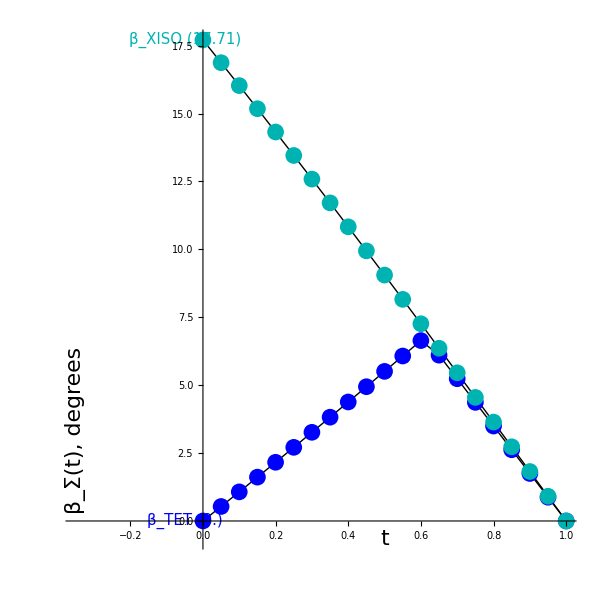

```mathematica
Graphics[{PointSize[.02],
line/@ListSigma,
{HueOfΣ[#],BetaCurve[Ranget,#]}&/@ListSigma,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{HueOfΣ[#],15}], (* the text *)
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@ListSigma,  (* the location of the text *)
Text[Style["β_Σ(t), degrees",22],{ylabelx,ylabely},{0,0},{0,1}], (* y-axis label *)
Text[Style["t",22],{xlabelx,xlabely},{0,0}] (* y-axis label *)
},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->600]
```

#### Pick one (your pick has to be from ListSigma)

```mathematica
Sig={TET};
```

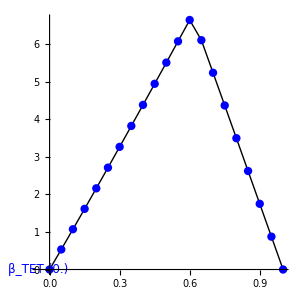

```mathematica
Graphics[{PointSize[.02],
line/@Sig,
{HueOfΣ[#],BetaCurve[Ranget,#]}&/@Sig,
Text[Style[SequenceForm[BetaText[#]," (",Round[βT[TT[tmin,Tmat1,Tmat2],#]/Degree,0.01],")"],{HueOfΣ[#],12}],
                                                {btextx,βT[TT[tmin,Tmat1,Tmat2],#]/Degree},{1,0}]&/@Sig},
Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->300]
```

## For reference

#### BrownNew: t=0 to t=1, dt = 0.05, ListSigma = all

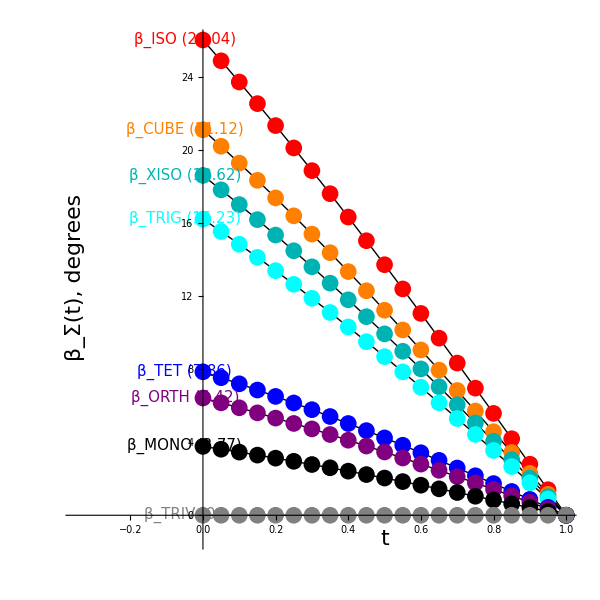

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

-Graphics-

#### BrownNew: dt = 0.05, Tmat1=TXISO, Tmat2=TTET, ListSigma = {TET,XISO}

-Graphics-

#### BrownTypo: dt = 0.05, Tmat1=TCUBE, Tmat2=TTET, ListSigma = {TET} NEEDS UPDATING

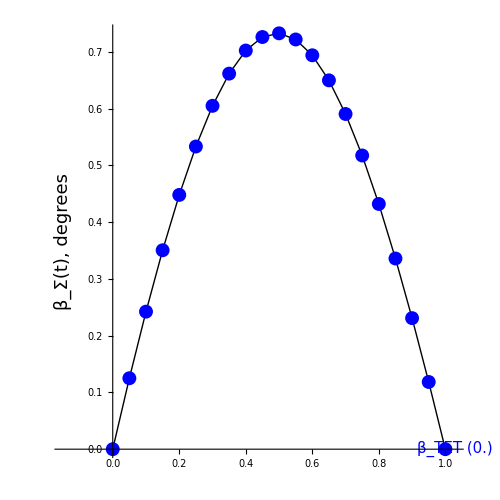

#### BrownNew: dt = 0.05, Tmat1=TCUBE, Tmat2=TTRIG, ListSigma = {TRIG,TET} NEEDS UPDATING